### Functions

```mathematica
(* Create an ordered list of -1,1, and 0 from an ordered list of integers.
A negative integer -n is replaced with n copies of -1, a positive integer n is replaced with n copies of 1, and 0 is left as is.
Example: {-3,0,0,4,1,-1,0}:>{-1,-1,-1,0,0,1,1,1,1,1,-1,0}*)
PopoList[list_List]:=Flatten@Map[Function[k,Table[Sign[k],{i,Max[Abs[k],1]}]],list]


(*Determine the label of a crossing by its position in the list of crossings, its order among the classical crossings, and its sign*)
XingLabel[xingPosn_,xingSgn_,classicalPosn_,n_] :=Module[{posnParity,orderParity},
posnParity = (-1)^(xingPosn+1); (*1 if odd, -1 if even*)
(*Base orientation for crossings is (k,k+n) (odd position and positive crossing or even and negative).
Reverse orientation is (k+n, k) (odd position and negative or even and positive) *)
orderParity = xingSgn * posnParity; (*1 if odd and positive or even and negative, -1 otherwise*)
result=Switch[orderParity,
1, {{xingSgn, classicalPosn, classicalPosn + n}},
-1, {{xingSgn, classicalPosn + n, classicalPosn}},
0, {}]
];

(* Create the rotation code {X, φ} of an arbitrary long rotational virtual popo knot (cut at the left lobe) from an ordered list of integers. Positive integers n correspond to n consecutive positive crossings, negative integers -n correspond to n consecutive negative crossings, and 0 corresponds to a virutal crossing.
Example: {1,0,-3,0,5} corresponds to the virtual popo knot starting with 1 positive crossing, a virtual crossing, 3 negative crossings, a virtual crossing, and 5 positive crossings.
Note that two lists may correspond to the same knot, e.g. {1,0,3,0,-2,0,3} and {1,0,1,1,1,0,-1,-1,0,2,1} 
Also, for the popo knot to be well-defined, it must have an odd number of total crossings. However, the way that the crossing labels are calculated assumes that there are 2n+1 crossings, so if only 2n crossings are represented in a list, a virtual crossing is implicitly inserted at the end of the list, e.g. {1,0,1,0} is effectively the same as {1,0,1,0,0}*)
PopoCodes[list_, k_:-1]:=Module[{popoList,xingList,indexedList,rotCode,n},
popoList=PopoList[list]; (**)
n=Total[Abs[popoList]]; (*Get the number of classical crossings*)
indexedList = Flatten[MapIndexed[Function[{sgn,i},If[sgn !=0, {{i[[1]],sgn}}, {}]], popoList],1]; 

Print[indexedList];(*Extract the classical crossings with their original index in popoList*)

xingList = Flatten[MapIndexed[Function[{l,i},XingLabel[l[[1]], l[[2]],i[[1]], n]], indexedList],1];
If[IntegerQ[k],
rotCode=Table[If[i==n+1,k,0],{i,2n+1}],
rotCode=k];
{xingList, rotCode}
];
```

```mathematica
(*Create the popocode obtained by gluing the top strand of popocode c_1 to the bottom strand of popocode c_2*)
PopoConcat[c1_,c2_]:=Module[{X1,X2,phi1,phi2,n1,X2shift, X3, phi2shift, phi3},
X1 = c1[[1]]; (*crossing list of c1*)
X2= c2[[1]]; (*crossing list of c2*)
phi1 =c1[[2]];(*rotation code of c1*)
phi2 =c2[[2]];(*rotation code of c1*)

(*Create the crossing list of c1 + c2 by concatenating the crossing lists of c1 and c2 after shifting the edge labels up by 2n1, where n1 is the number of classical crossings in c1*)
n1 = Total[Length[X1]];
X2shift=Map[Function[xing,{xing[[1]], xing[[2]]+2*n1, xing[[3]]+2*n1}], X2];
X3 = Join[X1,X2shift]; (*concatenated crossing list*)

(*Create the rotation code of c1 + c2 by concateneting them after combining strand 2n1+1 in c1 with strand 1 in c2*)
phi2shift = phi2[[2;;]]; (*include all but the first rotation number representing the 1st strand*)
phi3 = Join[phi1, phi2shift]; (*concatenated rotation code*)

(*Return the combined popocode*)
{X3, phi3}
];
```

```mathematica
(* Cycle the strand numbers of *)
```

```mathematica
XCycle[X_,k_]:=Module[{n},
n=Length[X]; (* Number of classical crossings is length of crossing list*)
X/.{x_[s_,i_,j_]:>{s,Mod[i+k-1,2n]+1,Mod[j+k-1,2n]+1}} (* Cycle the strand numbers by k *)
(* Need to split it up into k-1 and 1 because edges are not zero indexed *)
];
```

```mathematica
(* Reverse the orientation of the knot, preserving the chosen "1" strand *)
```

```mathematica
XReverse[X_]:=Module[{n},
n=Length[X]; (* Number of classical crossings is length of crossing list*)
X/.{x_[s_,i_,j_]:>{s,Mod[-(i-1),2n]+1,Mod[-(j-1),2n]+1}} (* Reverse the orientation by "negating" the strand numbers *)
(* Subtract then re-add 1 because edges are not zero indexed *)
]
```

```mathematica
Map[Function[X[s_,i_,j_], {s,Mod[i+1,4],Mod[j+1,4]},{{1,1,4},{1,2,3}}]]
```

Function::flpar: Parameter specification X[s_,i_,j_] in Function[X[s_,i_,j_],{s,Mod[i+1,4],Mod[j+1,4]},{{1,1,4},{1,2,3}}] should be a symbol or a list of symbols.

Map[Function[X[s_,i_,j_],{s,Mod[i+1,4],Mod[j+1,4]},{{1,1,4},{1,2,3}}]]

```mathematica
{{1,1,4},{1,2,3}}/.{X_[s_,i_,j_]:>{s,Mod[i,4]+1,Mod[j,4]+1}}
```

{{1,2,1},{1,3,4}}

#### Examples

```mathematica
e1=PopoCodes[Flatten@{Table[{-1,0},50],-1}]
```

{{1,-1},{3,-1},{5,-1},{7,-1},{9,-1},{11,-1},{13,-1},{15,-1},{17,-1},{19,-1},{21,-1},{23,-1},{25,-1},{27,-1},{29,-1},{31,-1},{33,-1},{35,-1},{37,-1},{39,-1},{41,-1},{43,-1},{45,-1},{47,-1},{49,-1},{51,-1},{53,-1},{55,-1},{57,-1},{59,-1},{61,-1},{63,-1},{65,-1},{67,-1},{69,-1},{71,-1},{73,-1},{75,-1},{77,-1},{79,-1},{81,-1},{83,-1},{85,-1},{87,-1},{89,-1},{91,-1},{93,-1},{95,-1},{97,-1},{99,-1},{101,-1}}

{{{-1,52,1},{-1,53,2},{-1,54,3},{-1,55,4},{-1,56,5},{-1,57,6},{-1,58,7},{-1,59,8},{-1,60,9},{-1,61,10},{-1,62,11},{-1,63,12},{-1,64,13},{-1,65,14},{-1,66,15},{-1,67,16},{-1,68,17},{-1,69,18},{-1,70,19},{-1,71,20},{-1,72,21},{-1,73,22},{-1,74,23},{-1,75,24},{-1,76,25},{-1,77,26},{-1,78,27},{-1,79,28},{-1,80,29},{-1,81,30},{-1,82,31},{-1,83,32},{-1,84,33},{-1,85,34},{-1,86,35},{-1,87,36},{-1,88,37},{-1,89,38},{-1,90,39},{-1,91,40},{-1,92,41},{-1,93,42},{-1,94,43},{-1,95,44},{-1,96,45},{-1,97,46},{-1,98,47},{-1,99,48},{-1,100,49},{-1,101,50},{-1,102,51}},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
x1=e1[[1]]
```

{{-1,52,1},{-1,53,2},{-1,54,3},{-1,55,4},{-1,56,5},{-1,57,6},{-1,58,7},{-1,59,8},{-1,60,9},{-1,61,10},{-1,62,11},{-1,63,12},{-1,64,13},{-1,65,14},{-1,66,15},{-1,67,16},{-1,68,17},{-1,69,18},{-1,70,19},{-1,71,20},{-1,72,21},{-1,73,22},{-1,74,23},{-1,75,24},{-1,76,25},{-1,77,26},{-1,78,27},{-1,79,28},{-1,80,29},{-1,81,30},{-1,82,31},{-1,83,32},{-1,84,33},{-1,85,34},{-1,86,35},{-1,87,36},{-1,88,37},{-1,89,38},{-1,90,39},{-1,91,40},{-1,92,41},{-1,93,42},{-1,94,43},{-1,95,44},{-1,96,45},{-1,97,46},{-1,98,47},{-1,99,48},{-1,100,49},{-1,101,50},{-1,102,51}}

```mathematica
XCycle[x1,2]
```

{{-1,54,3},{-1,55,4},{-1,56,5},{-1,57,6},{-1,58,7},{-1,59,8},{-1,60,9},{-1,61,10},{-1,62,11},{-1,63,12},{-1,64,13},{-1,65,14},{-1,66,15},{-1,67,16},{-1,68,17},{-1,69,18},{-1,70,19},{-1,71,20},{-1,72,21},{-1,73,22},{-1,74,23},{-1,75,24},{-1,76,25},{-1,77,26},{-1,78,27},{-1,79,28},{-1,80,29},{-1,81,30},{-1,82,31},{-1,83,32},{-1,84,33},{-1,85,34},{-1,86,35},{-1,87,36},{-1,88,37},{-1,89,38},{-1,90,39},{-1,91,40},{-1,92,41},{-1,93,42},{-1,94,43},{-1,95,44},{-1,96,45},{-1,97,46},{-1,98,47},{-1,99,48},{-1,100,49},{-1,101,50},{-1,102,51},{-1,1,52},{-1,2,53}}

### Theta

```mathematica
PD[epd_EPD]:=PD@@epd/.{Subscript[X, i_,j_]:>X[j,i+1,j+1,i],Subscript[X̄, i_,j_]:>X[j,i,j+1,i+1]}
```

```mathematica
Rot[{X_,φ_}]:={X,φ};
Rot[pd_PD]:=Module[{n,xs,x,rots,Xp,Xm,front={1},k},
n=Length@pd;rots=Table[0,{2n+1}];
xs=Cases[pd,x_X:>Piecewise[{{Xp[x⟦4⟧,x⟦1⟧], PositiveQ@x}, {Xm[x⟦2⟧,x⟦1⟧], True}}]];
For[k=1,k<=2n,++k,
If[FreeQ[front,-k],
front=Flatten@Replace[front,k->(xs/.{
Xp[k,l_]|Xm[l_,k]:>{l+1,k+1,-l},
Xp[l_,k]|Xm[k,l_]:>(++rots⟦l⟧;{-l,k+1,l+1}),
_Xp|_Xm:>{}
}), {1}],
Cases[front,k|-k]/.{k,-k}:>--rots⟦k⟧;
]
];
{xs/.{Xp[i_,j_]:>{+1,i,j}, Xm[i_,j_]:>{-1,i,j}},rots} ];
Rot[K_]:=Rot[PD[K]];
```

```mathematica
Options[PolyPlot1]={Labeled->False};PolyPlot1[Δ_,OptionsPattern[]]:=Module[{Δ1,crs,m,maxc,minc,s,rect},
Δ1=PowerExpand@Expand@Δ;
rect={{0,0},{1,0},{1,1},{0,1}};
If[Δ1===0,Graphics[],
m=Max[-Exponent[Δ1,T,Min], Exponent[Δ1,T,Max]];
crs=CoefficientRules[T^m Δ1,{T}];
maxc=N@Log@Max@Abs[Last/@crs];
minc=N@Log@Min@Select[Abs[Last/@crs],#>0&];
If[minc==maxc,s[_]=0,s[c_]:=s[c]=(maxc-Log@c)/(maxc-minc)];
Graphics[crs/.({x_}->c_):>{
Lighter[Which[c==0, White,c>0, Red,c<0,Blue], 0.88s[Abs@c]],
Tooltip[Polygon[({x+m-1/2,0}+#)&/@rect],c T^(x-m)],
If[Not@OptionValue[Labeled],{},{Black, FontSize->Scaled[1/((m+1)(6+maxc))],Text[c T^(x-m),{x+m,0.5}]}]
},AspectRatio->Min[1/5 ,1/√(m+1)],ImagePadding->None,PlotRangePadding->None]
]];
Options[PolyPlot2]={Labeled->False, Shear->True};
PolyPlot2[θ_,OptionsPattern[]]:=Module[{θ1,crs,m1,m2,maxc,minc,s,stone,mat,p},
θ1=PowerExpand@Expand@θ;
If[θ1===0,Graphics[{White,Disk[]}],
If[OptionValue[Shear],
stone=Table[{Cos[α],Sin[α]}/Cos[2π/12]/2, {α,2π/12,2π,2π/6}];
mat=({{1, -1/2}, {0, √3/2}}),
stone={{1,1}, {-1,1},{-1,-1},{1,-1}}/2;
mat=IdentityMatrix[2];
];
m1=Max[-Exponent[θ1,Subscript[T, 1],Min], Exponent[θ1,Subscript[T, 1],Max]];
m2=Max[-Exponent[θ1,Subscript[T, 2],Min], Exponent[θ1,Subscript[T, 2],Max]];
crs=CoefficientRules[Subscript[T, 1]^m1 Subscript[T, 2]^m2 θ1,{Subscript[T, 1],Subscript[T, 2]}];
maxc=N@Log@Max@Abs[Last/@crs];
minc=N@Log@Min@Select[Abs[Last/@crs],#>0&];
If[minc==maxc,s[_]=0,s[c_]:=s[c]=(maxc-Log@c)/(maxc-minc)];
Graphics[{(*{Yellow,Disk[{0,0},1+Cos[2π/12]Norm[{m1,m2}]/√2]},*)
crs/.({x1_,x2_}->c_):>{
Lighter[Which[c==0, White,c>0, Red,c<0,Blue], 0.88s[Abs@c]],
p=mat.{x1-m1,x2-m2};
Tooltip[Polygon[(p+#)&/@stone],c Subscript[T, 1]^(x1-m1)Subscript[T, 2]^(x2-m2)] ,
If[Not@OptionValue[Labeled],{},{Black, FontSize->Scaled[1/(Max[m1,m2](10+maxc))],Text[c Subscript[T, 1]^(x1-m1)Subscript[T, 2]^(x2-m2),p]}]
}
},ImagePadding->None,PlotRangePadding->None]
]];
Options[PolyPlot]={Labeled->False, ImageSize->Automatic};
PolyPlot[{Δ_,θ_},opts___Rule]:=GraphicsColumn[
{PolyPlot1[Δ,FilterRules[Join[{opts},Options[PolyPlot]],Options[PolyPlot1]]],
PolyPlot2[θ,FilterRules[Join[{opts},Options[PolyPlot]],Options[PolyPlot2]]]},
Spacings -> Scaled@0.08,ImagePadding->None,PlotRangePadding->None,
FilterRules[Join[{opts},Options[PolyPlot]],Options[GraphicsColumn]]
];
```

```mathematica
CF[ℰ_] := Expand@Collect[ℰ,Subscript[g, __],F]/.F->Factor;
```

```mathematica
Subscript[T, 3]=Subscript[T, 1] Subscript[T, 2];
```

```mathematica
Subscript[F, 1][{s_,i_,j_}]:=CF[
s(1/2-Subscript[g, 3,i,i]+Subscript[T, 2]^s Subscript[g, 1,i,i] Subscript[g, 2,j,i]-Subscript[g, 1,i,i] Subscript[g, 2,j,j]-(Subscript[T, 2]^s-1)Subscript[g, 2,j,i] Subscript[g, 3,i,i]+2 Subscript[g, 2,j,j] Subscript[g, 3,i,i]-(1-Subscript[T, 3]^s)Subscript[g, 2,j,i] Subscript[g, 3,j,i]-Subscript[g, 2,i,i] Subscript[g, 3,j,j]-Subscript[T, 2]^s Subscript[g, 2,j,i] Subscript[g, 3,j,j]+Subscript[g, 1,i,i] Subscript[g, 3,j,j]+((Subscript[T, 1]^s-1)Subscript[g, 1,j,i](Subscript[T, 2]^(2s)Subscript[g, 2,j,i]-Subscript[T, 2]^s Subscript[g, 2,j,j]+Subscript[T, 2]^s Subscript[g, 3,j,j])+(Subscript[T, 3]^s-1)Subscript[g, 3,j,i](1-Subscript[T, 2]^s Subscript[g, 1,i,i]+Subscript[g, 2,i,j]+(Subscript[T, 2]^s-2)Subscript[g, 2,j,j]-(Subscript[T, 1]^s-1)(Subscript[T, 2]^s+1) Subscript[g, 1,j,i]))/(Subscript[T, 2]^s-1))]
```

```mathematica
Subscript[F, 2][{s0_,i0_,j0_},{s1_,i1_,j1_}]:=CF[s1(Subscript[T, 1]^s0-1)(Subscript[T, 2]^s1-1)^-1(Subscript[T, 3]^s1-1)Subscript[g, 1,j1,i0] Subscript[g, 3,j0,i1]( (Subscript[T, 2]^s0 Subscript[g, 2,i1,i0]-Subscript[g, 2,i1,j0])- (Subscript[T, 2]^s0 Subscript[g, 2,j1,i0]-Subscript[g, 2,j1,j0]))]
```

```mathematica
Subscript[F, 3][φ_,k_]=φ Subscript[g, 3,k,k]-φ/2;
```

```mathematica
Θ[K_]:=Θ[K]=Module[{X,φ,n,A,Δ,G,ev,θ,k,k1,k2},
(* 1 *) {X,φ}=Rot[K]; n=Length[X]; A=IdentityMatrix[2n+1];
(* 2 *) Cases[X,{s_,i_,j_}:>(A⟦{i,j},{i+1,j+1}⟧+=({{-T^s, T^s-1}, {0, -1}}))];
(* 3 *) Δ=T^((-Total[φ]-Total[X⟦All,1⟧])/2)Det[A];
(* 4 *) G=Inverse[A];
(* 5 *) ev[ℰ_]:=Factor[ℰ/.Subscript[g, ν_,α_,β_]:>(G⟦α,β⟧/.T->Subscript[T, ν])];
(* 6 *) θ=ev[Sum[Subscript[F, 1][X⟦k⟧], {k,n}]];
(* 7 *) θ+=ev[Sum[Subscript[F, 2][X[[k1]],X[[k2]]], {k1,n}, {k2,n}]];
(* 8 *) θ+=ev[Sum[Subscript[F, 3][φ[[k]],k], {k,Length@φ}]];
(* 9 *) Factor@{Δ,(Δ/.T->Subscript[T, 1])(Δ/.T->Subscript[T, 2])(Δ/.T->Subscript[T, 3])θ}
];
```

```mathematica
A[K_]:=A[K]=Module[{X,φ,n,A,Δ,G,ev,θ,k,k1,k2,SumF1,SumF2,SumF3,NormTheta,NormF1,NormF2,NormF3},
(* 1 *) {X,φ}=Rot[K]; n=Length[X]; A=IdentityMatrix[2n+1];
(* 2 *) Cases[X,{s_,i_,j_}:>(A⟦{i,j},{i+1,j+1}⟧+=({{-T^s, T^s-1}, {0, -1}}))];
(* 3 *) Δ=T^((-Total[φ]-Total[X⟦All,1⟧])/2)Det[A];
(* 4 *) G=Inverse[A];
{A,G}
];
```

```mathematica
NormF1[K_]:=NormF1[K]=Module[{X,φ,n,A,Δ,G,ev,θ,k,k1,k2,SumF1},
(* 1 *) {X,φ}=Rot[K]; n=Length[X]; A=IdentityMatrix[2n+1];
(* 2 *) Cases[X,{s_,i_,j_}:>(A⟦{i,j},{i+1,j+1}⟧+=({{-T^s, T^s-1}, {0, -1}}))];
(* 3 *) Δ=T^((-Total[φ]-Total[X⟦All,1⟧])/2)Det[A];
(* 4 *) G=Inverse[A];
(* 5 *) ev[ℰ_]:=Factor[ℰ/.Subscript[g, ν_,α_,β_]:>(G⟦α,β⟧/.T->Subscript[T, ν])];
(* 6 *) SumF1=ev[Sum[Subscript[F, 1][X⟦k⟧], {k,n}]];
(*   *) {Δ,(Δ/.T->Subscript[T, 1])(Δ/.T->Subscript[T, 2])(Δ/.T->Subscript[T, 3])SumF1};
SumF1
];
NormF2[K_]:=NormF1[K]=Module[{X,φ,n,A,Δ,G,ev,θ,k,k1,k2,SumF2},
(* 1 *) {X,φ}=Rot[K]; n=Length[X]; A=IdentityMatrix[2n+1];
(* 2 *) Cases[X,{s_,i_,j_}:>(A⟦{i,j},{i+1,j+1}⟧+=({{-T^s, T^s-1}, {0, -1}}))];
(* 3 *) Δ=T^((-Total[φ]-Total[X⟦All,1⟧])/2)Det[A];
(* 4 *) G=Inverse[A];
(* 5 *) ev[ℰ_]:=Factor[ℰ/.Subscript[g, ν_,α_,β_]:>(G⟦α,β⟧/.T->Subscript[T, ν])];
(* 6 *) SumF2=ev[Sum[Subscript[F, 2][X[[k1]],X[[k2]]], {k1,n}, {k2,n}]];
(*   *) {Δ,(Δ/.T->Subscript[T, 1])(Δ/.T->Subscript[T, 2])(Δ/.T->Subscript[T, 3])SumF2};
SumF2
];
```

```mathematica
NormF3[K_]:=NormF1[K]=Module[{X,φ,n,A,Δ,G,ev,θ,k,k1,k2,SumF3},
(* 1 *) {X,φ}=Rot[K]; n=Length[X]; A=IdentityMatrix[2n+1];
(* 2 *) Cases[X,{s_,i_,j_}:>(A⟦{i,j},{i+1,j+1}⟧+=({{-T^s, T^s-1}, {0, -1}}))];
(* 3 *) Δ=T^((-Total[φ]-Total[X⟦All,1⟧])/2)Det[A];
(* 4 *) G=Inverse[A];
(* 5 *) ev[ℰ_]:=Factor[ℰ/.Subscript[g, ν_,α_,β_]:>(G⟦α,β⟧/.T->Subscript[T, ν])];
(* 6 *) SumF3=ev[Sum[Subscript[F, 3][φ[[k]],k], {k,Length@φ}]];
(*   *) {Δ,(Δ/.T->Subscript[T, 1])(Δ/.T->Subscript[T, 2])(Δ/.T->Subscript[T, 3])SumF3};
SumF3
];
```

### Examples

```mathematica
e2=PopoCodes[Flatten@{Table[{-1,0},10],-1}]
```

{{1,-1},{3,-1},{5,-1},{7,-1},{9,-1},{11,-1},{13,-1},{15,-1},{17,-1},{19,-1},{21,-1}}

{{{-1,12,1},{-1,13,2},{-1,14,3},{-1,15,4},{-1,16,5},{-1,17,6},{-1,18,7},{-1,19,8},{-1,20,9},{-1,21,10},{-1,22,11}},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Θ[e2]
```

{1/T^5,1/(T_1^10 T_2^10)(-5+T_2-T_1 T_2+T_2^2-T_1^2 T_2^2+T_2^3-T_1^3 T_2^3+T_2^4-T_1^4 T_2^4+T_2^5-T_1^5 T_2^5+T_2^6-T_1^6 T_2^6+T_2^7-T_1^7 T_2^7+T_2^8-T_1^8 T_2^8+T_2^9-T_1^9 T_2^9+T_2^10-T_1^10 T_2^10+T_1 T_2^11+T_1^2 T_2^11+T_1^3 T_2^11+T_1^4 T_2^11+T_1^5 T_2^11+T_1^6 T_2^11+T_1^7 T_2^11+T_1^8 T_2^11+T_1^9 T_2^11+T_1^10 T_2^11-2 T_1 T_2^12+2 T_1^11 T_2^12-2 T_1^2 T_2^13+2 T_1^11 T_2^13-2 T_1^3 T_2^14+2 T_1^11 T_2^14-2 T_1^4 T_2^15+2 T_1^11 T_2^15-2 T_1^5 T_2^16+2 T_1^11 T_2^16-2 T_1^6 T_2^17+2 T_1^11 T_2^17-2 T_1^7 T_2^18+2 T_1^11 T_2^18-2 T_1^8 T_2^19+2 T_1^11 T_2^19-2 T_1^9 T_2^20+2 T_1^11 T_2^20-2 T_1^10 T_2^21+2 T_1^11 T_2^21)}

```mathematica
b=Factor[Simplify[(Θ[e2][[1]]/.T->Subscript[T, 1])(Θ[e2][[1]]/.T->Subscript[T, 2])(Θ[e2][[1]]/.T->Subscript[T, 3])(NormF3[e2]+NormF2[e2]+NormF1[e2])]]
```

1/(2 T_1^10 (-1+T_2) T_2^10)(-1+T_2-4 T_1 T_2+4 T_1^2 T_2-4 T_1 T_2^2+4 T_1^2 T_2^2-4 T_1^3 T_2^2+4 T_1^4 T_2^2-4 T_1^3 T_2^3+4 T_1^4 T_2^3-4 T_1^5 T_2^3+4 T_1^6 T_2^3-4 T_1^5 T_2^4+4 T_1^6 T_2^4-4 T_1^7 T_2^4+4 T_1^8 T_2^4-4 T_1^7 T_2^5+4 T_1^8 T_2^5-4 T_1^9 T_2^5+4 T_1^10 T_2^5-4 T_1^9 T_2^6+4 T_1^10 T_2^6-4 T_1^11 T_2^6+4 T_1^12 T_2^6-4 T_1^11 T_2^7+4 T_1^12 T_2^7-4 T_1^13 T_2^7+4 T_1^14 T_2^7-4 T_1^13 T_2^8+4 T_1^14 T_2^8-4 T_1^15 T_2^8+4 T_1^16 T_2^8-4 T_1^15 T_2^9+4 T_1^16 T_2^9-4 T_1^17 T_2^9+4 T_1^18 T_2^9-4 T_1^17 T_2^10+4 T_1^18 T_2^10-4 T_1^19 T_2^10+4 T_1^20 T_2^10+4 T_2^11+4 T_1 T_2^11+4 T_1^2 T_2^11+4 T_1^3 T_2^11+4 T_1^4 T_2^11+4 T_1^5 T_2^11+4 T_1^6 T_2^11+4 T_1^7 T_2^11+4 T_1^8 T_2^11+4 T_1^9 T_2^11+4 T_1^10 T_2^11+2 T_1^11 T_2^11-4 T_1^12 T_2^11-4 T_1^13 T_2^11-4 T_1^14 T_2^11-4 T_1^15 T_2^11-4 T_1^16 T_2^11-4 T_1^17 T_2^11-4 T_1^18 T_2^11-8 T_1^19 T_2^11-8 T_1^21 T_2^11-4 T_1 T_2^12-4 T_1^2 T_2^12-4 T_1^3 T_2^12-4 T_1^4 T_2^12-4 T_1^5 T_2^12-4 T_1^6 T_2^12-4 T_1^7 T_2^12-4 T_1^8 T_2^12-4 T_1^9 T_2^12-4 T_1^10 T_2^12-2 T_1^11 T_2^12+4 T_1^12 T_2^12+4 T_1^13 T_2^12+4 T_1^14 T_2^12+4 T_1^15 T_2^12+4 T_1^16 T_2^12+4 T_1^17 T_2^12+4 T_1^18 T_2^12+4 T_1^19 T_2^12+4 T_1^20 T_2^12+4 T_1^22 T_2^12)

```mathematica
e2
```

{{{-1,12,1},{-1,13,2},{-1,14,3},{-1,15,4},{-1,16,5},{-1,17,6},{-1,18,7},{-1,19,8},{-1,20,9},{-1,21,10},{-1,22,11}},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
e3={e2[[1]],Table[0,2*Length[e2[[1]]]+1]}
```

{{{-1,12,1},{-1,13,2},{-1,14,3},{-1,15,4},{-1,16,5},{-1,17,6},{-1,18,7},{-1,19,8},{-1,20,9},{-1,21,10},{-1,22,11}},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

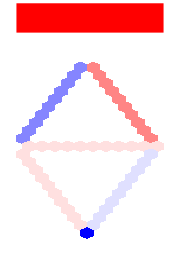

```mathematica
PolyPlot[Θ[e3],ImageSize->Small]
```

```mathematica
e4={XCycle[e3[[1]],12],e3[[2]]}
```

{{{-1,2,13},{-1,3,14},{-1,4,15},{-1,5,16},{-1,6,17},{-1,7,18},{-1,8,19},{-1,9,20},{-1,10,21},{-1,11,22},{-1,12,1}},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

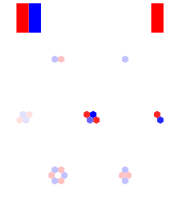

```mathematica
PolyPlot[Θ[e4],ImageSize->Small]
```

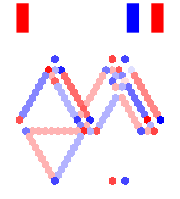

```mathematica
e5={XCycle[e3[[1]],20],e3[[2]]}; PolyPlot[Θ[e5],ImageSize->Small]
```